# MATH 263 Numerical differential equations

Ethan Smith

## Lecture 9: BVPs and shooting method. 8 APR 2021

## Assigned reading for next time.

Zill, Section 9.5.

## Method implementations.

Disclaimer: The implementations below are not efficient in Mathematica, but they have been chosen for pedagogical reasons.

```mathematica
euler[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n]},
{x[0],y[0]} =N[ {a,y0}];
Do[
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*f[x[i],y[i]];,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]]
];
```

```mathematica
heun[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n],k1,k2,w1=0.5,w2=0.5},
{x[0],y[0]} = N[{a,y0}];
Do[
k1=f[x[i],y[i]];
k2=f[x[i]+h,y[i]+h*k1];
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(w1*k1 + w2*k2);,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]]
];
```

```mathematica
rk4[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n], k1, k2, k3, k4, w1=1./6, w2=1./3, w3=1./3,w4=1./6},
{x[0],y[0]} = N[{a,y0}];
Do[
k1=f[x[i],y[i]];
k2=f[x[i]+0.5*h,y[i]+0.5*h*k1];
k3=f[x[i]+0.5*h,y[i]+0.5*h*k2];
k4=f[x[i]+h,y[i]+h*k3];
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(w1*k1+w2*k2+w3*k3+w4*k4);,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

```mathematica
ab2[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n],dy1,dy2},
{{x[0],y[0]},{x[1],y[1]}}=heun[f,a,a+h,y0,1];
dy2=f[x[0],y[0]];
Do[
dy1=f[x[i],y[i]];
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(3*dy1-dy2)/2;
(*Shift f evals down to get ready for next step.  Could be done without actually moving the data, but not worth the effort here.*)
dy2=dy1;,
{i,1,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

```mathematica
abm2[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n],yhat,dy0,dy1,dy2},
{{x[0],y[0]},{x[1],y[1]}}=heun[f,a,a+h,y0,1];
dy2=f[x[0],y[0]];
Do[
dy1=f[x[i],y[i]];
x[i+1]=x[i]+h;
yhat=y[i]+h*(3*dy1-dy2)/2; (*predict*)
dy0=f[x[i+1],yhat];
y[i+1]=y[i]+h*(dy0+dy1)/2; (*correct*)
(*Shift f evals down to get ready for next step.  Could be done without actually moving the data, but not worth the effort here.*)
dy2=dy1;,
{i,1,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

## Boundary value problems.

Side conditions must be imposed in order for a system of ODE’s to have a unique a solution.  If all the side conditions are imposed as a single point, then the problem is called an initial value problem (IVP).  If the side conditions are imposed at more than one point, then we have a boundary value problem (BVP).  In typical situations, the conditions are imposed at the endpoints (boundary) of an interval [a,b], which of course explains the name.  

Since higher-order equations can be expressed as systems of first order equations, we can restrict attention to problems of the form

y’=f(x,y), a≤x≤b,

g(y(a),y(b))=0,

where, as usual, bold symbols denote vectors of the appropriate dimension.

## Shooting method.

The shooting method is a trick for turning this type of problem into a “sequence” of problems that we already know how to solve.  The idea is to replace the BVP by an IVP with unknown parameters.  In particular, we ignore any conditions imposed on y(b) by the boundary condition (2).  Then we fix any values of the vector y(a) that can be determined from the start; the rest we treat as unknowns.  We then “guess” the unknown parameters in y(a) and solve the resulting IVP.  We then check to see if numerical result satisfies (2) to within desired tolerance.

## Example.

Consider the second-order BVP

y’’ =4y, y(0)=0, y(1)=5.

Solve the BVP exactly.

```mathematica
Clear[x,y]
f[x_,y_,Dy_]=4*y;
{a,b}={0,1};
{alpha,beta}={0,5};
Y[x_]=y[x]/.DSolve[{y''[x]==f[x,y[x],y'[x]],y[a]==alpha,y[b]==beta},y[x],x][[1]]//FullSimplify;
Print[StringForm["The exact solution to the BVP is ``.",TraditionalForm[y[x]==Y[x]]]];
```

The exact solution to the BVP is y(x)==(10 ⅇ^2 sinh(2 x))/(ⅇ^4-1).

Transform the BVP into a family of IVPs with a free parameter.  Then solve the BVP by the shooting method using our RK4 solver with step-size h=0.1.

We first transform the BVP into the form of equations (1) and (2).  First we transform the ODE y''=4y into a first order system of the form (1).  For this we introduce the variables u_1=y, u_2=y' so that the equation in (1) can be written as

u_1'=u_2,
          u_2'=4 u_1.

Collecting the variables into the vector-valued functions  u=(u_1
u_2) , f(x,u) = (u_2
4 u_1), and g(u_1(0), u_1(1)) = (u_1(0)-0
u_2(1)-5), the entire BVP may now be written in the form of (1) and (2).  

For the shooting method, we ignore what the condition g(u_1(0), u_1(1)) = (u_1(0)-0
u_2(1)-5) =(0
0) has to say about u at x=1.  This gives us the IVP problem

u’=f(x,u),
u(0)=(u_1(0)
u_2(0)) = (0
s),

where s is a parameter to be chosen so that u_1(1)=5 (at least approximately).

```mathematica
Clear[x,u,u1,u2,s];
u[x_]={u1[x],u2[x]};
F[x_,u_]:={u[[2]], f[x,u[[1]],u[[2]]]};
Clear[u0]
u0[s_]={0,s};
{a,b}={0,1};
h=0.1;
n=(b-a)/h;
target=5;
```

First, we just guess.  Let’s go with s=1.

{0.,0.100667,0.205373,0.318322,0.444047,0.587591,0.754718,0.952133,1.18776,1.47106,1.81339}

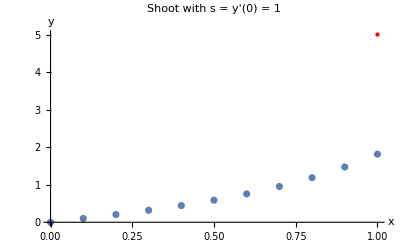

Too low

```mathematica
s=1;
approxSoln=rk4[F,a,b,u0[s],n];
mesh=approxSoln[[All,1]];
approxY=approxSoln[[All,2,1]]

Show[
ListPlot[Transpose[Join[{mesh,approxY}]]],
Graphics[{Red,PointSize[Large],Point[{b,target}]}],
PlotRange->All,
AxesLabel->{x,y},
PlotLabel->StringForm["Shoot with s = y'(``) = ``",a,s]
]

If[Last[approxSoln][[2,1]]<target,Print["Too low"],Print["Too high"]];
```

It looks like we should try a steeper slope.  Let’s guess much higher value for s=u_2(0)=y'(0).  How about s=3?

{0.,0.302,0.61612,0.954967,1.33214,1.76277,2.26415,2.8564,3.56328,4.41317,5.44016}

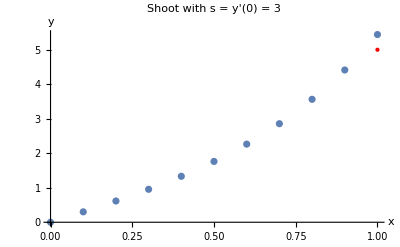

Too high

```mathematica
s=3;
approxSoln=rk4[F,a,b,u0[s],n];
mesh=approxSoln[[All,1]];
approxY=approxSoln[[All,2,1]]

Show[
ListPlot[Transpose[Join[{mesh,approxY}]]],
Graphics[{Red,PointSize[Large],Point[{b,target}]}],
PlotRange->All,
AxesLabel->{x,y},
PlotLabel->StringForm["Shoot with s = y'(``) = ``",a,s]
]

If[Last[approxSoln][[2,1]]<target,Print["Too low"],Print["Too high"]];
```

Now we have “bracketed” s.  In particular, we “know” (assuming that the problem varies continuously with s) that s∈[1,3].  Now, we can bisect the interval and guess s=(1+3)/2=2.  If that guess is too low, we know that s∈[2,3].  If it is too high, we know that s∈[1,2].  We can keep iterating/bisecting until we get within some desired tolerance of our target y(1)=5.  Let’s see if we can get 3 decimal places.

Tolerance achieved with s = 2.75732.

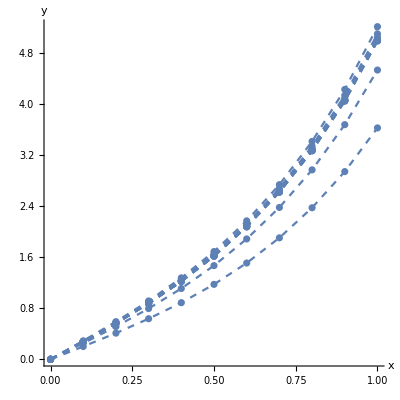

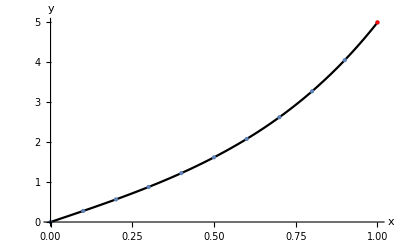

```mathematica
TOL=N[10^(-4)];
{slow,shigh}={1.,3};
Block[{notDone=1,y1,s,plt},
Clear[plt];
plt=Graphics[{Red,PointSize[Large],Point[{b,target}]},Axes->True,AxesLabel->{x,y}];
While[notDone==1,
s=(slow+shigh)/2;
approxSoln=rk4[F,a,b,u0[s],n];
mesh=approxSoln[[All,1]];
approxY=approxSoln[[All,2,1]];

plt=Show[plt,ListPlot[Transpose[Join[{mesh,approxY}]],Joined->True,PlotStyle->{Dashed},Mesh->All],PlotRange->All];

y1=Last[approxSoln][[2,1]];
If[Abs[target-y1]<TOL,
Print[StringForm["Tolerance achieved with s = ``.",s]];
Print[Show[plt,AspectRatio->1]];
notDone=0;,
If[target<y1,shigh=s;,slow=s;];
];
];
];



Show[
Plot[Y[x],{x,a,b},PlotStyle->Black],
ListPlot[Transpose[Join[{mesh,approxY}]],PlotStyle->PointSize[Large]],
Graphics[{Red,PointSize[Large],Point[{b,target}]}],
PlotRange->All,
AxesLabel->{x,y}
]
```